In this notebook we expand quantities related to the boost of γ_0.

```mathematica
<<peeters` ;
<<MaTeX`
<<GA13`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 14]
peeters`setGitDir[ "../project/figures/classicalmechanics" ]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→14,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

\\wsl$\Ubuntu\home\pjoot\project\figures\classicalmechanics

```mathematica
ClearAll[vcap, r]
vcap=Bivector[1, 1,0];
g0 = Vector[1,0];
r[alpha_] := Cosh[alpha] + vcap Sinh[alpha]
x[a_] = r[a] ** g0;
xt[a_] := D[x[b],b]/. b -> a;
x[α]
xt[α]
(xt[α].xt[α])//Simplify
```

Cosh[α] γ_0+Sinh[α] γ_1

Sinh[α] γ_0+Cosh[α] γ_1

-1+4 0.0

Same thing in coordinates, but but the time coordinate second so that we plot it “up”.

```mathematica
xc[a_] = {Cosh[a], Sinh[a]} // Reverse;
xct[a_] = {Sinh[a], Cosh[a]} // Reverse;
G = DiagonalMatrix[{-1,1}] ;
xc[a].G.xct[a]
xc[a].G.xc[a] // Simplify
xct[a].G.xct[a] // Simplify
```

0

1

-1

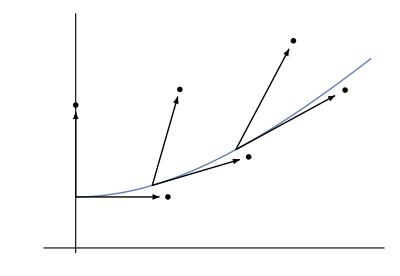

```mathematica
o = {0,0};
alphas = {0,0.3,0.6};
p = Show[{
ParametricPlot[
xc[a],
{a,0,1},
PlotStyle->Thick,
PlotRange->{{-0.1,1.2},{0.8,1.7}},
Ticks-> None,
AxesLabel-> {MaTeX["x"],MaTeX["c t"]}
],
Graphics[{
Thick,
Arrow[{xc[#],4xc[#]/3}] &/@alphas,
Arrow[{xc[#], xc[#] + xct[#]/3}]&/@alphas,
Text[MaTeX["x(\\alpha)"], 1.02   4xc[#]/3] &/@alphas,
Text[MaTeX["\\mathbf{x}_\\alpha"], xc[#] + 1.1 xct[#]/3] &/@alphas
}]
}]
```